```mathematica
EtaRExp[x0_,a_,x_]:=-(1+a (1-Exp[-x/x0]))
```

```mathematica
EtaRLin[x0_,a_,x_]:=-If[x<x0,1+a x/x0,1+a]
```

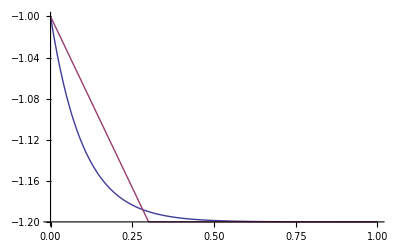

```mathematica
Plot[{EtaRExp[.1,0.2,x],EtaRLin[.3,0.2,x]},{x,0,1}, PlotRange->All]
```